```mathematica
data1=Import["C:\\Users\\Ziwei Ma\\Downloads\\network_aging_codes_2018-master\\1.kaeberlein04plos\\kaeberlein04_selected_strains.csv"];
data2=Import["C:\\Users\\Ziwei Ma\\Downloads\\network_aging_codes_2018-master\\1.kaeberlein04plos\\kaeberlein04_selected_strains1.csv"];
```

```mathematica
d2=Import["C:\\Users\\Ziwei Ma\\Downloads\\network_aging_codes_2018-master\\1.kaeberlein04plos\\sir2.csv"];
d3=Import["C:\\Users\\Ziwei Ma\\Downloads\\network_aging_codes_2018-master\\1.kaeberlein04plos\\glocus2.csv"];
d4=Import["C:\\Users\\Ziwei Ma\\Downloads\\network_aging_codes_2018-master\\1.kaeberlein04plos\\fob1.csv"];
d5=Import["C:\\Users\\Ziwei Ma\\Downloads\\network_aging_codes_2018-master\\1.kaeberlein04plos\\hxk2.csv"];
d6=Import["C:\\Users\\Ziwei Ma\\Downloads\\network_aging_codes_2018-master\\1.kaeberlein04plos\\fob1hxk2.csv"];
```

```mathematica
nameData
```

{fig1b.BY4742,fig2a.sir2,fig4b.by4742.SIR2.ox.2glucose,fig1b.fob1,fig1b.hxk2,fig1b.fob1.hxk2}

```mathematica
data2[[All,1]]
```

{4,5,7,8,9,9,10,10,10,10,11,11,12,12,13,13,14,14,15,15,15,15,15,15,15,15,15,16,16,16,16,16,17,17,17,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,20,20,20,20,20,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,27,27,27,27,27,27,27,27,27,27,27,28,28,28,28,28,28,28,28,28,28,28,28,28,29,29,29,29,29,29,29,29,29,29,29,29,29,29,30,30,30,30,30,30,31,31,31,31,31,31,31,31,31,31,31,31,31,32,32,32,32,32,32,32,32,33,33,33,33,33,34,34,34,34,34,34,35,35,35,35,35,35,35,36,36,36,37,37,37,37,37,38,38,38,38,38,38,40,40,40,41,41,42,42,42,42,42,43,43,44,45,47,48,48,49,50,51,51,52,52,57}

```mathematica
d6[[All,1]]
```

{6,7,9,9,10,12,13,13,13,14,14,15,16,18,18,18,19,19,19,19,20,21,22,23,26,27,27,28,28,28,28,29,29,29,29,30,30,31,31,31,32,32,33,34,34,34,34,34,35,36,37,37,38,39,39,39,40,40,40,40,41,41,41,42,42,42,43,43,44,45,45,45,45,46,46,46,46,46,46,48,50,50,51,51,51,51,52,53,53,53,53,53,53,54,54,54,55,55,55,57,57,58,58,58,58,59,59,59,60,60,60,61,61,61,62,62,62,62,63,63,64,66,66,66,66,66,66,67,67,68,70,70,70,71,73,73,73,73,74,74,74,74,75,75,76,77,77,78,78,79,79,83,83,85,89,89,89,93,94,96}

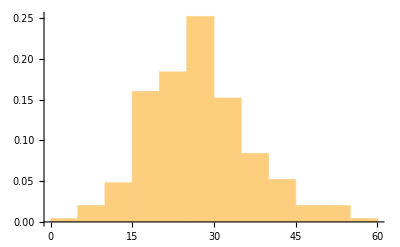
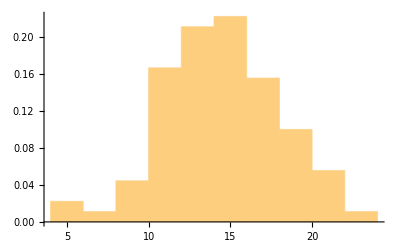
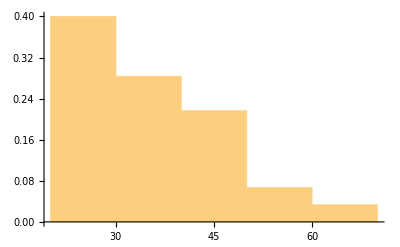
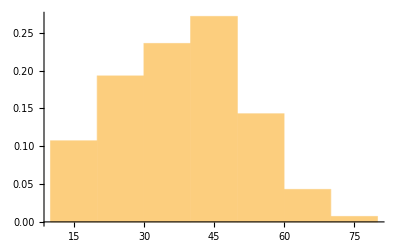
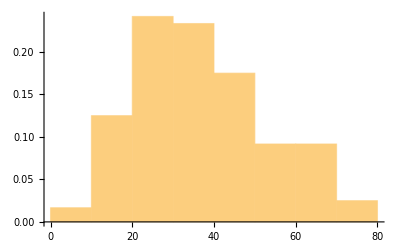
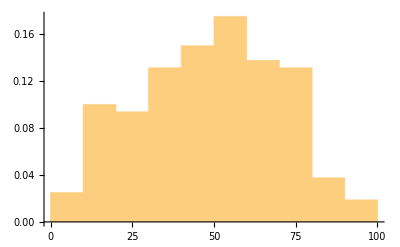

```mathematica
Table[Histogram[data2[[All,i]],Automatic,"Probability"],{i,{1,2,3,4,5,6}}]
```

```mathematica
𝒟1=SurvivalDistribution[data2[[All,1]]];
𝒟2=SurvivalDistribution[d2[[All,1]]];𝒟3=SurvivalDistribution[d3[[All,1]]];𝒟4=SurvivalDistribution[d4[[All,1]]];𝒟5=SurvivalDistribution[d5[[All,1]]];𝒟6=SurvivalDistribution[d6[[All,1]]];
```

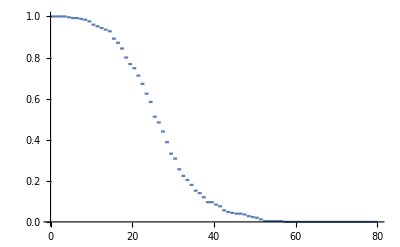

```mathematica
Plot[SurvivalFunction[𝒟1,x],{x,0,80}]
```

```mathematica
𝒮=SurvivalModelFit[data2[[All,1]]];
𝒮2=SurvivalModelFit[d2[[All,1]]];
𝒮3=SurvivalModelFit[d3[[All,1]]];
𝒮4=SurvivalModelFit[d4[[All,1]]];
𝒮5=SurvivalModelFit[d5[[All,1]]];
𝒮6=SurvivalModelFit[d6[[All,1]]];
```

```mathematica
d2new=Permute[d2[[All,1]],RandomPermutation[90]]
```

{9,17,15,10,23,15,13,11,11,14,16,18,13,10,12,12,14,21,9,11,20,13,18,12,15,13,15,18,18,16,20,17,13,17,16,15,13,9,15,14,18,16,10,18,14,16,13,14,14,13,15,12,9,21,11,5,16,12,13,11,10,15,18,11,13,11,13,12,16,21,16,14,10,6,18,15,11,14,14,14,19,16,15,12,12,11,17,10,16,5}

```mathematica
𝒮2new=SurvivalModelFit[d2new];
```

Power::infy: Infinite expression 1/0. encountered.

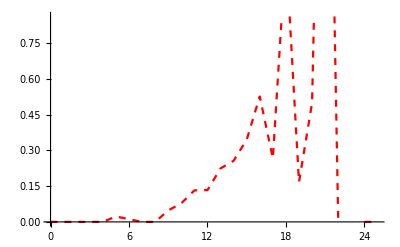

```mathematica
HF21new=ListPlot[Table[{a,𝒮2new["HF"][a]},{a,0,25}],Joined->True,PlotStyle->{Red,Dashed}]
```

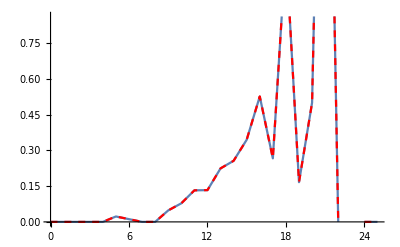

```mathematica
Show[HF21,HF21new]
```

```mathematica
Length[data2[[All,1]]]
```

250

Power::infy: Infinite expression 1/0. encountered.

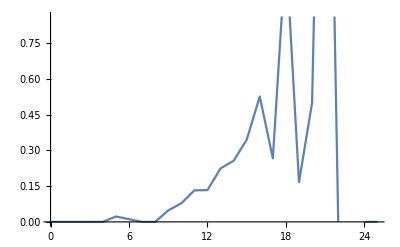

```mathematica
HF21=ListPlot[Table[{a,𝒮2["HF"][a]},{a,0,25}],Joined->True]
```

Power::infy: Infinite expression 1/0. encountered.

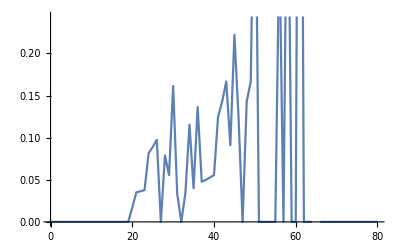

```mathematica
HF3=ListPlot[Table[{a,𝒮3["HF"][a]},{a,0,80}],Joined->True]
```

```mathematica
𝒮["HF"][40]
```

0.142857

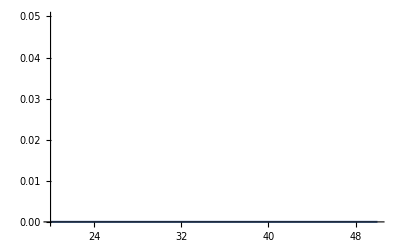

```mathematica
Plot[𝒮["HF"][x],{x,20,50},Exclusions->None]
```

```mathematica
𝒮["HF"][46]
```

0.

```mathematica
𝒮["HF"][x]//PiecewiseExpand
```

Power::infy: Infinite expression 1/0. encountered.

Piecewise[{{0., 4<x<5∨5<x<7∨7<x<8∨8<x<9∨9<x<10∨10<x<11∨11<x<12∨12<x<13∨13<x<14∨14<x<15∨15<x<16∨16<x<17∨17<x<18∨18<x<19∨19<x<20∨20<x<21∨21<x<22∨22<x<23∨23<x<24∨24<x<25∨25<x<26∨26<x<27∨27<x<28∨28<x<29∨29<x<30∨30<x<31∨31<x<32∨32<x<33∨33<x<34∨34<x<35∨35<x<36∨36<x<37∨37<x<38∨38<x<40∨40<x<41∨41<x<42∨42<x<43∨43<x<44∨44<x<45∨45<x<47∨47<x<48∨48<x<49∨49<x<50∨50<x<51∨51<x<52∨52<x<57∨x<4}, {0.00401606, x==4}, {0.00403226, x==5}, {0.00404858, x==7}, {0.00406504, x==8}, {0.00819672, x==9}, {0.00840336, x==11}, {0.00847458, x==12}, {0.00854701, x==13}, {0.00862069, x==14}, {0.0166667, x==10}, {0.0229358, x==16}, {0.026738, x==20}, {0.0331754, x==17}, {0.0403587, x==15}, {0.0416667, x==19}, {0.0505618, x==21}, {0.055, x==18}, {0.0578512, x==26}, {0.0595238, x==22}, {0.0684932, x==24}, {0.0769231, x==23}, {0.0779221, x==30}, {0.0857143, x==36}, {0.0909091, x==44}, {0.0980392, x==33}, {0.1, x==27}, {0.1, x==45}, {0.105263, x==41}, {0.111111, x==47}, {0.133333, x==34}, {0.134021, x==28}, {0.140625, x==25}, {0.142857, x==40}, {0.142857, x==32}, {0.166667, x==43∨x==49}, {0.166667, x==37}, {0.168675, x==29}, {0.184211, x==35}, {0.2, x==50}, {0.203125, x==31}, {0.25, x==38}, {0.285714, x==48}, {0.357143, x==42}, {0.666667, x==51}, {2., x==52}, {ComplexInfinity, x==57}}]

Power::infy: Infinite expression 1/0. encountered.

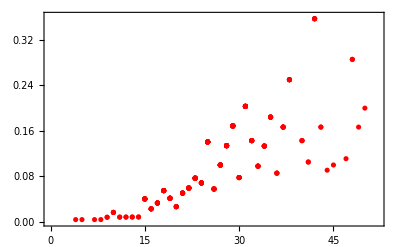

```mathematica
HF1=ListPlot[Table[{a,𝒮["HF"][a]},{a,data2[[All,1]]}],PlotStyle->{Red, Thick},Frame->True]
```

Power::infy: Infinite expression 1/0. encountered.

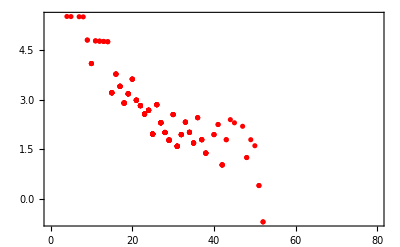

```mathematica
HF1L=ListPlot[Table[{a,-Log[𝒮["HF"][a]]},{a,data2[[All,1]]}],PlotStyle->{Red, Thick},PlotRange->{{0,80},All},Frame->True]
```

```mathematica
hf1=Table[{a,𝒮["HF"][a]},{a,data2[[All,1]]}];
e𝒟1=EstimatedDistribution[data2[[All,1]],GompertzMakehamDistribution[λ,ξ,θ,α]]
```

Power::infy: Infinite expression 1/0. encountered.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

GompertzMakehamDistribution[0.0464701,0.0741631,0.0129904,6.41387]

```mathematica
e𝒟1a=EstimatedDistribution[data2[[All,1]],GompertzMakehamDistribution[λ,ξ]]
```

GompertzMakehamDistribution[0.0854466,0.0769792]

```mathematica
PDF[GompertzMakehamDistribution[λ,ξ,θ,α],x]
```

Piecewise[{{λ ξ (θ+2 α λ x+ⅇ^(λ x)) ⅇ^(ξ (-(α λ^2 x^2+θ λ x+ⅇ^(λ x)-1))), x≥0}, {0, True}}]

```mathematica
e𝒟1Q=GompertzMakehamDistribution[,ξ]
```

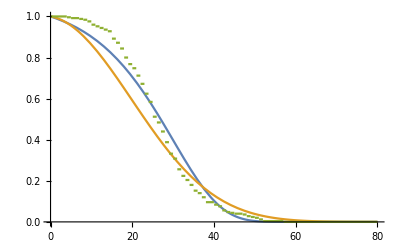

```mathematica
pdf1=Plot[{1-CDF[e𝒟1a,x],1-CDF[e𝒟1,x],SurvivalFunction[𝒟1,x]},{x,0,80}]
```

Power::infy: Infinite expression 1/0. encountered.

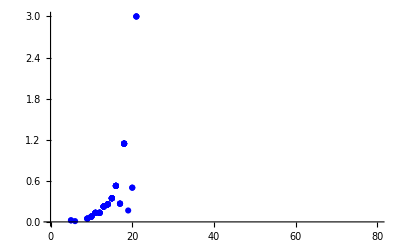

```mathematica
HF2=ListPlot[Table[{a,𝒮2["HF"][a]},{a,d2[[All,1]]}],PlotStyle->{Blue, Thick},PlotRange->{{0,80},All}]
```

Power::infy: Infinite expression 1/0. encountered.

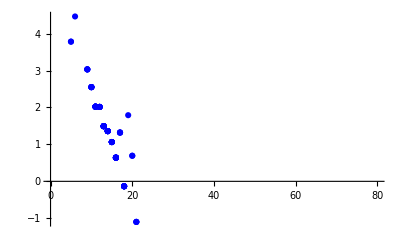

```mathematica
HF2L=ListPlot[Table[{a,-Log[𝒮2["HF"][a]]},{a,d2[[All,1]]}],PlotStyle->{Blue, Thick},PlotRange->{{0,80},All}]
```

Power::infy: Infinite expression 1/0. encountered.

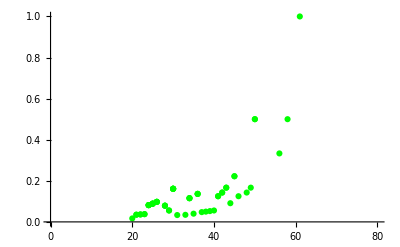

```mathematica
HF3=ListPlot[Table[{a,𝒮3["HF"][a]},{a,d3[[All,1]]}],PlotStyle->{Green, Thick},PlotRange->{{0,80},All}]
```

Power::infy: Infinite expression 1/0. encountered.

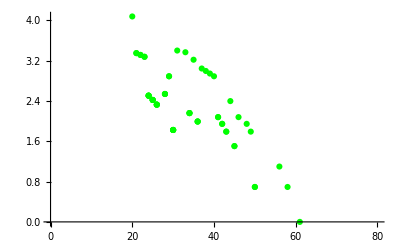

```mathematica
HF3L=ListPlot[Table[{a,-Log[𝒮3["HF"][a]]},{a,d3[[All,1]]}],PlotStyle->{Green, Thick},PlotRange->{{0,80},All}]
```

Power::infy: Infinite expression 1/0. encountered.

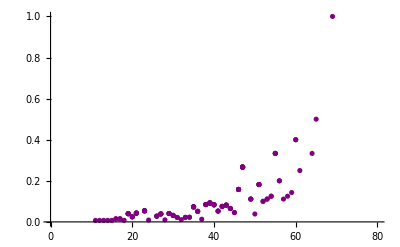

```mathematica
HF4=ListPlot[Table[{a,𝒮4["HF"][a]},{a,d4[[All,1]]}],PlotStyle->{Purple, Thick},PlotRange->{{0,80},All}]
```

Power::infy: Infinite expression 1/0. encountered.

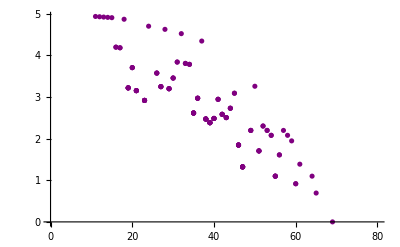

```mathematica
HF4L=ListPlot[Table[{a,-Log[𝒮4["HF"][a]]},{a,d4[[All,1]]}],PlotStyle->{Purple, Thick},PlotRange->{{0,80},All}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

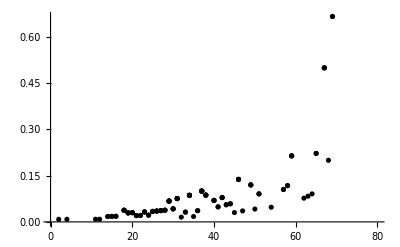

```mathematica
HF5=ListPlot[Table[{a,𝒮5["HF"][a]},{a,d5[[All,1]]}],PlotStyle->{Black, Thick},PlotRange->{{0,80},All}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

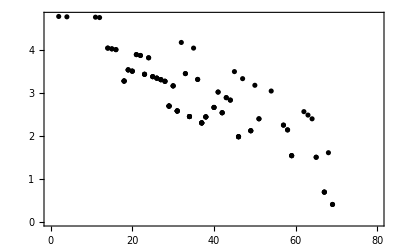

```mathematica
HF5L=ListPlot[Table[{a,-Log[𝒮5["HF"][a]]},{a,d5[[All,1]]}],PlotStyle->{Black, Thick},PlotRange->{{0,80},All},Frame->True]
```

Power::infy: Infinite expression 1/0. encountered.

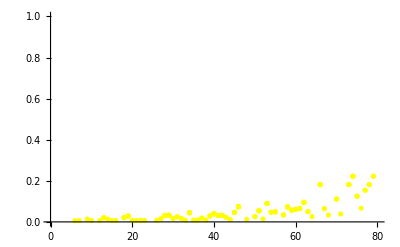

```mathematica
HF6=ListPlot[Table[{a,𝒮6["HF"][a]},{a,d6[[All,1]]}],PlotStyle->{Yellow, Thick},PlotRange->{{0,80},All}]
```

Power::infy: Infinite expression 1/0. encountered.

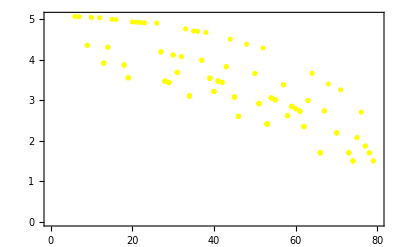

```mathematica
HF6L=ListPlot[Table[{a,-Log[𝒮6["HF"][a]]},{a,d6[[All,1]]}],PlotStyle->{Yellow, Thick},PlotRange->{{0,80},All},Frame->True]
```

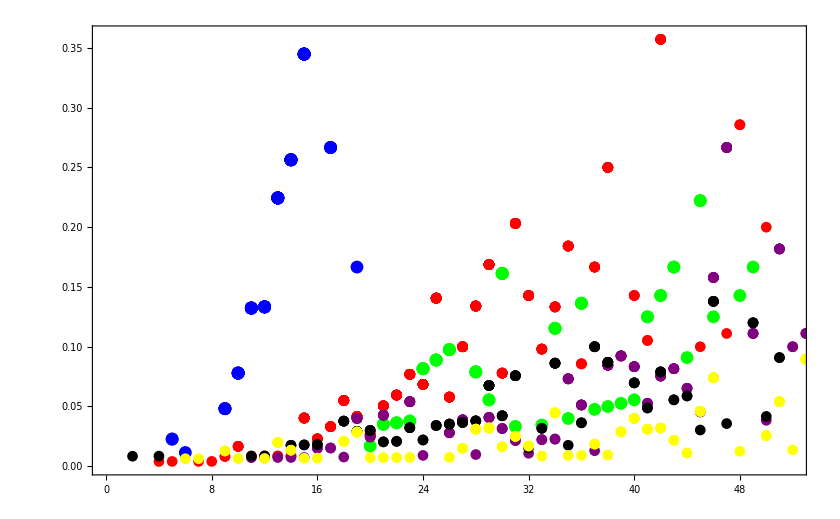

```mathematica
Show[HF1,HF2,HF3,HF4,HF5,HF6]
```

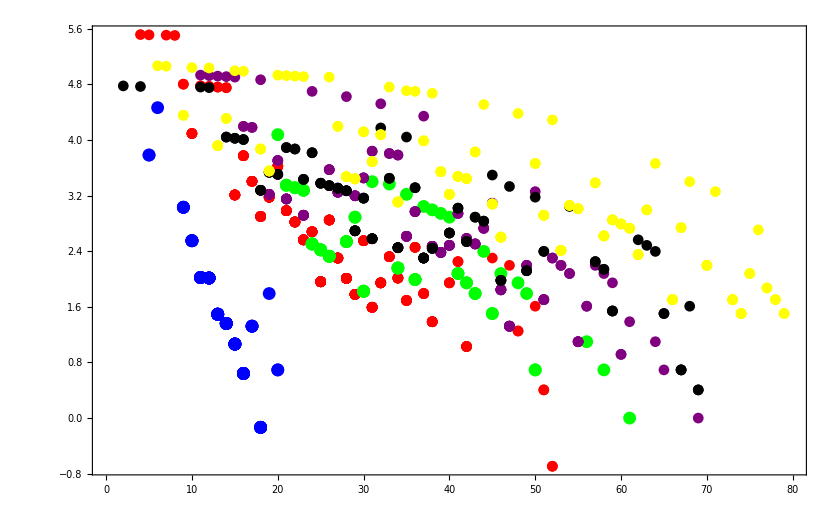

```mathematica
Show[HF1L,HF2L,HF3L,HF4L,HF5L,HF6L]
```

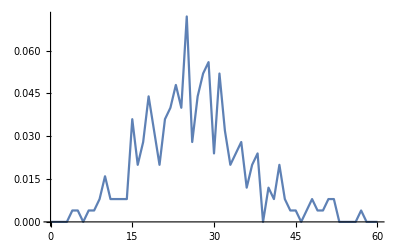

```mathematica
ListPlot[Table[{a,𝒮["PDF"][a]},{a,0,60}],Joined->True]
```

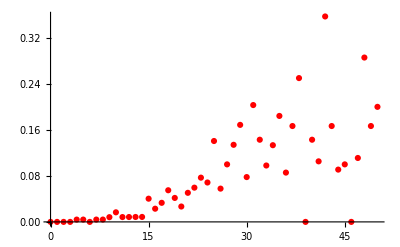

```mathematica
HF2=ListPlot[Table[{a,𝒮["PDF"][a]/(1-𝒮["CDF"][a])},{a,0,50}],PlotRange->All,PlotStyle->{Red,Thick}]
```

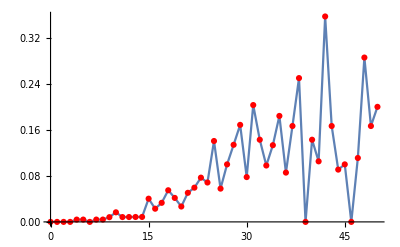

```mathematica
Show[HF1,HF2]
```

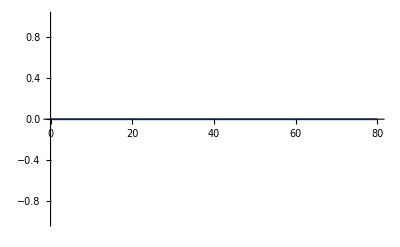

```mathematica
Plot[HazardFunction[𝒟1,x],{x,0,80}]
```

```mathematica
Attributes[data2]
```

{}

```mathematica
data22=Delete[data2[[All,2]],"#NA"]
```

Delete::psl: Position specification #NA in {5,5,6,9,9,9,9,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,«200»} is not a machine-sized integer or a list of machine-sized integers.

Delete[{5,5,6,9,9,9,9,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,17,17,17,17,18,18,18,18,18,18,18,18,19,20,20,21,21,21,23,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA},#NA]

```mathematica
SurvivalFunction[𝒟1,x]//PiecewiseExpand
```

Piecewise[{{0., x≥57}, {0.004, 52≤x<57}, {0.012, 51≤x<52}, {0.02, 50≤x<51}, {0.024, 49≤x<50}, {0.028, 48≤x<49}, {0.036, 47≤x<48}, {0.04, 45≤x<47}, {0.044, 44≤x<45}, {0.048, 43≤x<44}, {0.056, 42≤x<43}, {0.076, 41≤x<42}, {0.084, 40≤x<41}, {0.096, 38≤x<40}, {0.12, 37≤x<38}, {0.14, 36≤x<37}, {0.152, 35≤x<36}, {0.18, 34≤x<35}, {0.204, 33≤x<34}, {0.224, 32≤x<33}, {0.256, 31≤x<32}, {0.308, 30≤x<31}, {0.332, 29≤x<30}, {0.388, 28≤x<29}, {0.44, 27≤x<28}, {0.484, 26≤x<27}, {0.512, 25≤x<26}, {0.584, 24≤x<25}, {0.624, 23≤x<24}, {0.672, 22≤x<23}, {0.712, 21≤x<22}, {0.748, 20≤x<21}, {0.768, 19≤x<20}, {0.8, 18≤x<19}, {0.844, 17≤x<18}, {0.872, 16≤x<17}, {0.892, 15≤x<16}, {0.928, 14≤x<15}, {0.936, 13≤x<14}, {0.944, 12≤x<13}, {0.952, 11≤x<12}, {0.96, 10≤x<11}, {0.976, 9≤x<10}, {0.984, 8≤x<9}, {0.988, 7≤x<8}, {0.992, 5≤x<7}, {0.996, 4≤x<5}, {1., True}}]

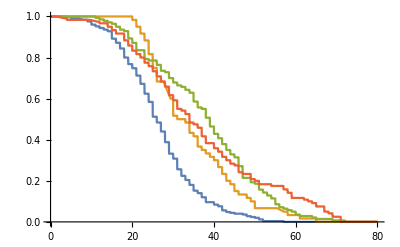

```mathematica
Plot[{SurvivalFunction[𝒟1,x],SurvivalFunction[𝒟3,x],SurvivalFunction[𝒟4,x],SurvivalFunction[𝒟5,x]},{x,0,80},Exclusions->None]
```

```mathematica
Plot[Table[SurvivalDistribution[𝒟,x],{𝒟,{𝒟1,𝒟2,𝒟3,𝒟4,𝒟5,𝒟6}}],{x,0,100}]
```

-Graphics-

```mathematica
Plot[SurvivalDistribution[𝒟1,x],{x,0,60}]
```

-Graphics-

```mathematica
Plot[{SurvivalDistribution[𝒟1,x],SurvivalDistribution[𝒟2,x]},{x,0,60}]
```

-Graphics-